# DSolve Assignment

### Instructions

The purpose of this assignment is to assess your ability to use DSolve command to solve differential equations in Mathematica. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

## Solve the differential equation dy/dx = 4y+2 with each of the initial conditions shown below.

a) y(0) = 2

```mathematica
d:=DSolveValue[{y'[x]==4y[x]+2,y[0]==#},y[x],x]&;
y1[x_]=d[2]
```

1/2 (-1+5 ⅇ^(4 x))

b) y(0) = 3

```mathematica
y2[x_]=d[3]
```

1/2 (-1+7 ⅇ^(4 x))

c) y(0) = 5

```mathematica
y3[x_]=d[5]
```

1/2 (-1+11 ⅇ^(4 x))

d) Plot each of the above solutions.

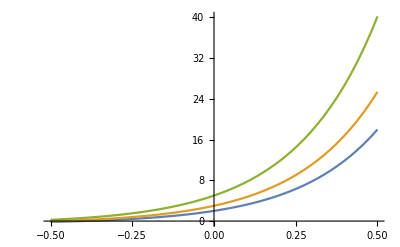

```mathematica
Plot[{y1[x],y2[x],y3[x]},{x,-.5,.5}]
```

(e) The above examples have you calculate different solutions to the differential equation based on different initial conditions. The difference in the conditions is just a vertical shift. Do the solutions also differ only by a vertical shift? Briefly describe how the above solution curves reflect the equations that represent them.

Text your answer here: The solutions to differential equations vertically shift only on the y axis while the rest of the curve follows a different path on the slope field for this specific case.